## Initialization

```mathematica
(*<<"/Users/rdbeer/Dropbox/Mathematica/Dynamica/Dynamica.m"*)
```

```mathematica
<<"/Users/LJSbo/Documents/Wolfram Mathematica/Dynamica.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
Dynamica`Private`MakeBPGraphics[b_,λ_,z_,s_]:=
With[{p=Join[{λ/.Dynamica`Private`DSParameterSubsts[Dynamica`Private`BPDynamicalSystem[b]]},Dynamica`Private`BPPoint[b]⟦z⟧],t=Dynamica`Private`BPType[b]},
Point[Join[{λ/.Dynamica`Private`DSParameterSubsts[Dynamica`Private`BPDynamicalSystem[b]]},p]];
Which[
t===Branch,Join[s,{Point[p],Text["B",p,{3,0}]}],
t===Fold,Join[s,{Point[p],Text["F",p,{3,0}]}],
t===Hopf,Join[s,{Point[p],Text["H",p,{3,0}]}],
t===NeutralSaddle,Join[s,{Point[p],Text["N",p,{3,0}]}],
True,{}]];
```

HP on dynamical system

```mathematica
τbidx = 20;
σ[x_]=1/(1+ⅇ^-x);
ρ[z_]=Piecewise[{{(.25-z)/.25,z<.25},{(.75-z)/.25,z>.75}}];
```

```mathematica
CTRNN2yHPon= DynamicalSystem[{(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2])/τ1,(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2])/τ2, ρ[σ[y1+θ1]]/τb},
{{y1,-16,16},{y2,-16,16},{θ1,-16,16}},
{{w11,-16,16},{w12,-16,16},{w21,-16,16},{w22,-16,16},{θ2,-16,16},{τ1,0.5,10},{τ2,0.5,10},{τb,10,40}}];
```

```mathematica
With[{ε=10^-13}, 
CTRNN2oHPon= TransformDynamicalSystem[CTRNN2yHPon,{{o1,ε,1-ε},{o2,ε,1-ε},{θ1new,-16,16}},{σ[y1+θ1],σ[y2+θ2],θ1}]];
```

HP off dynamical system

```mathematica
CTRNN2yHPoff= DynamicalSystem[{(-y1+w11 σ[y1+θ1]+w21 σ[y2+θ2])/τ1,(-y2+w12 σ[y1+θ1]+w22 σ[y2+θ2])/τ2},
{{y1,-16,16},{y2,-16,16}},
{{w11,-16,16},{w12,-16,16},{w21,-16,16},{w22,-16,16},{θ1,-16,16},{θ2,-16,16},{τ1,0.5,10},{τ2,0.5,10}}];
```

```mathematica
With[{ε=10^-9}, 
CTRNN2oHPoff= TransformDynamicalSystem[CTRNN2yHPoff,{{o1,ε,1-ε},{o2,ε,1-ε}},{σ[y1+θ1],σ[y2+θ2]}]];
```

## Figure 1

```mathematica
(*Circuit parameters*)
τ1idx = 1.70843;
τ2idx = 9.64855;
θ1init = 9.27502;
θ2idx = 6.16402;
w11idx = 6.01381;
w12idx = 11.421;
w21idx = -6.90268;
w22idx = -2.00297;
```

```mathematica
(*Substitute in parameters*)
CTRNN2oHPoff=CTRNN2oHPoff/.{w11->w11idx,w12->w12idx,w21->w21idx,w22->w22idx,θ1->θ1init,θ2->θ2idx,τ1->τ1idx,τ2->τ2idx};
CTRNN2oHPon=CTRNN2oHPon/.{w11->w11idx,w12->w12idx,w21->w21idx,w22->w22idx,θ2->θ2idx,τ1->τ1idx,τ2->τ2idx,τb->τbidx};
```

```mathematica
(*Make Plot*)
Show[
DisplayBifurcationDiagram[CTRNN2oHPoff,θ1,MaxSteps->Infinity,PlotRange->{{-2,5},{0,1},{0.8,1}},AxesStyle->Directive[Black,12]],
Graphics3D[{PointSize[0.02],Point[{3.47682531,0.785551,0.999998}],Text["F",{3.47682531,0.785551,0.999998},{3,0}]}],
Graphics3D[{Orange,Thickness[0.008],Line[Map[{#[[3]],#[[1]],#[[2]]}&,Dynamica`Private`TrajectorySegment[Trajectory[CTRNN2oHPon,{0.9036150245668311,0.9999992069964184,3.6589179491348376},97],97]]]}],
DisplayTrajectories[CTRNN2oHPon,{{.8,.8,-1.63349}},150,Arrows->4,StateVariables->{θ1new,o1,o2},PlotStyle->Directive[Orange,Opacity[1],Thickness[0.003]]]]
```

-Graphics3D-

## Figure 2

```mathematica
(*Circuit parameters*)
τ1idx = 4.19982;
τ2idx = 2.81508;
θ1init = -10;
θ2idx = -1.5239;
w11idx = 12.7138;
w12idx = -12.0723;
w21idx = 7.86948;
w22idx = 12.3104;
```

```mathematica
(*Substitute in parameters*)
CTRNN2oHPoff=CTRNN2oHPoff/.{w11->w11idx,w12->w12idx,w21->w21idx,w22->w22idx,θ1->θ1init,θ2->θ2idx,τ1->τ1idx,τ2->τ2idx};
CTRNN2oHPon=CTRNN2oHPon/.{w11->w11idx,w12->w12idx,w21->w21idx,w22->w22idx,θ2->θ2idx,τ1->τ1idx,τ2->τ2idx,τb->τbidx};
```

```mathematica
(*Find HPoff Limit Cycle and follow branches*)
LCHPoff=FindLimitCycle[CTRNN2oHPoff,{0.0008394077147273316,0.06592547413428092},47];
LCBHPoff=FollowLimitCycleBranch[LCHPoff,θ1,MaxStepSize->0.08];
```

```mathematica
(*Make Plot*)
Show[
DisplayBifurcationDiagram[CTRNN2oHPoff,θ1,MaxSteps->Infinity,LimitCycleBranches->{Take[LCBHPoff,{25,61}][[2;; ;;2]]},PlotRange->{{-15,-3.5},{0,1},{0,1}},AxesStyle->Directive[Black,12]],
Graphics3D[{PointSize[0.02],Point[{-11.3272346,0.0906689,0.999938}],Text["F",{-11.3272346,0.0906689,0.999938},{3,0}]}],
DisplayTrajectories[CTRNN2oHPon,{{0.18181244147030493,0.9999048390847736,-9.368902104788939}},90,Arrows->0,StateVariables->{θ1new,o1,o2},PlotStyle->Directive[Orange,Thickness[0.02]]],
DisplayTrajectories[CTRNN2oHPon,{{.5,.85,-5}},250,MaxSteps->10000,Arrows->0,StateVariables->{θ1new,o1,o2},PlotStyle->Directive[Orange, Opacity[1],Thickness[0.003]]]]
```

-Graphics3D-

## Figure 3

```mathematica
(*Circuit parameters*)
τ1idx = 2.38904;
τ2idx = 5.69255;
θ1init = -2.97092;
θ2idx = -5.85415;
w11idx = 8.70451;
w12idx = 3.80029;
w21idx = -6.33088;
w22idx = 5.27963;
```

```mathematica
(*Substitute in parameters*)
CTRNN2oHPoff=CTRNN2oHPoff/.{w11->w11idx,w12->w12idx,w21->w21idx,w22->w22idx,θ1->θ1init,θ2->θ2idx,τ1->τ1idx,τ2->τ2idx};
CTRNN2oHPon=CTRNN2oHPon/.{w11->w11idx,w12->w12idx,w21->w21idx,w22->w22idx,θ2->θ2idx,τ1->τ1idx,τ2->τ2idx,τb->τbidx};
```

```mathematica
DisplayTrajectories[CTRNN2oHPoff,{{.3,.5}},900]
```

DisplayTrajectories[TransformDynamicalSystem[DynamicalSystem[{0.585333 (6.01381/(1+ⅇ^(-9.27502-y1))-6.90268/(1+ⅇ^(-6.16402-y2))-y1),0.103643 (11.421/(1+ⅇ^(-9.27502-y1))-2.00297/(1+ⅇ^(-6.16402-y2))-y2)},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+ⅇ^(-9.27502-y1)),1/(1+ⅇ^(-6.16402-y2))}],{{0.3,0.5}},900]

```mathematica
(*Find HPoff Limit Cycle and follow branches - Can't get it to stay in the very small oscillatory region, always jumps to the big one*)
LCHPoff=FindLimitCycle[CTRNN2oHPoff,Last[First[$Trajectories]],47];

LCBHPoff=FollowLimitCycleBranch[LCHPoff,θ1,MaxStepSize->0.01,MinStepSize->0.001];
```

First::normal: Nonatomic expression expected at position 1 in First[$Trajectories].

```mathematica
DisplayPhasePortrait[CTRNN2oHPoff,LimitSets->{LCHPoff},Tries->100]
```

DisplayPhasePortrait[TransformDynamicalSystem[DynamicalSystem[{0.585333 (6.01381/(1+ⅇ^(-9.27502-y1))-6.90268/(1+ⅇ^(-6.16402-y2))-y1),0.103643 (11.421/(1+ⅇ^(-9.27502-y1))-2.00297/(1+ⅇ^(-6.16402-y2))-y2)},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+ⅇ^(-9.27502-y1)),1/(1+ⅇ^(-6.16402-y2))}],LimitSets→{FindLimitCycle[TransformDynamicalSystem[DynamicalSystem[{0.585333 (6.01381/(1+ⅇ^(-9.27502-y1))-6.90268/(1+ⅇ^(-6.16402-y2))-y1),0.103643 (11.421/(1+ⅇ^(-9.27502-y1))-2.00297/(1+ⅇ^(-6.16402-y2))-y2)},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+ⅇ^(-9.27502-y1)),1/(1+ⅇ^(-6.16402-y2))}],$Trajectories,47]},Tries→100]

```mathematica
Length[LCBHPoff]
```

4

```mathematica
DisplayBifurcationDiagram[CTRNN2oHPoff,θ1,MaxSteps->Infinity,LimitCycleBranches->{Join[LCBHPoff[[1;;45]][[2;; ;;2]],LCBHPoff[[46;;300]][[10;; ;;10]],LCBHPoff[[300;;322]][[1;; ;;1]]]},PlotRange->{{-6,1},{0,1},{0,1}},AxesStyle->Directive[Black,12]]
(*DisplayBifurcationDiagram[CTRNN2oHPoff,θ1,MaxSteps->Infinity,LimitCycleBranches->{LCBHPoff},PlotRange->{{-6,1},{0,1},{0,1}},AxesStyle->Directive[Black,12]]*)
```

Part::take: Cannot take positions 1 through 45 in FollowLimitCycleBranch[FindLimitCycle[TransformDynamicalSystem[DynamicalSystem[{0.585333 (Times[«2»]+Times[«2»]+Times[«2»]),0.103643 (Times[«2»]+Times[«2»]+Times[«2»])},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+ⅇ^Plus[«2»]),1/(1+ⅇ^Plus[«2»])}],$Trajectories,47],θ1,MaxStepSize→0.01,MinStepSize→0.001].

Part::take: Cannot take positions 46 through 300 in FollowLimitCycleBranch[FindLimitCycle[TransformDynamicalSystem[DynamicalSystem[{0.585333 (Times[«2»]+Times[«2»]+Times[«2»]),0.103643 (Times[«2»]+Times[«2»]+Times[«2»])},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+ⅇ^Plus[«2»]),1/(1+ⅇ^Plus[«2»])}],$Trajectories,47],θ1,MaxStepSize→0.01,MinStepSize→0.001].

Part::take: Cannot take positions 10 through -1 in FollowLimitCycleBranch[FindLimitCycle[TransformDynamicalSystem[DynamicalSystem[{0.585333 Plus[«3»],0.103643 Plus[«3»]},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+Power[«2»]),1/(1+Power[«2»])}],$Trajectories,47],θ1,MaxStepSize→0.01,MinStepSize→0.001]⟦46;;300⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Join::heads: Heads Span and Part at positions 1 and 2 are expected to be the same.

DisplayBifurcationDiagram[TransformDynamicalSystem[DynamicalSystem[{0.585333 (6.01381/(1+ⅇ^(-9.27502-y1))-6.90268/(1+ⅇ^(-6.16402-y2))-y1),0.103643 (11.421/(1+ⅇ^(-9.27502-y1))-2.00297/(1+ⅇ^(-6.16402-y2))-y2)},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+ⅇ^(-9.27502-y1)),1/(1+ⅇ^(-6.16402-y2))}],θ1,MaxSteps→∞,LimitCycleBranches→{Join[1;;45,FollowLimitCycleBranch[FindLimitCycle[TransformDynamicalSystem[DynamicalSystem[{0.585333 (6.01381/(1+ⅇ^(-9.27502-y1))-6.90268/(1+ⅇ^(-6.16402-y2))-y1),0.103643 (11.421/(1+ⅇ^(-9.27502-y1))-2.00297/(1+ⅇ^(-6.16402-y2))-y2)},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+ⅇ^(-9.27502-y1)),1/(1+ⅇ^(-6.16402-y2))}],$Trajectories,47],θ1,MaxStepSize→0.01,MinStepSize→0.001]⟦46;;300⟧⟦10;;All;;10⟧,FollowLimitCycleBranch[FindLimitCycle[TransformDynamicalSystem[DynamicalSystem[{0.585333 (6.01381/(1+ⅇ^(-9.27502-y1))-6.90268/(1+ⅇ^(-6.16402-y2))-y1),0.103643 (11.421/(1+ⅇ^(-9.27502-y1))-2.00297/(1+ⅇ^(-6.16402-y2))-y2)},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+ⅇ^(-9.27502-y1)),1/(1+ⅇ^(-6.16402-y2))}],$Trajectories,47],θ1,MaxStepSize→0.01,MinStepSize→0.001]⟦300;;322⟧]},PlotRange→{{-6,1},{0,1},{0,1}},AxesStyle→Directive[GrayLevel[0],12]]

```mathematica
(*Make Plot*)
Show[
DisplayBifurcationDiagram[CTRNN2oHPoff,θ1,MaxSteps->Infinity,LimitCycleBranches->{Join[LCBHPoff[[1;;45]][[2;; ;;2]],LCBHPoff[[46;;300]][[10;; ;;10]],LCBHPoff[[300;;322]][[1;; ;;1]]]},PlotRange->{{-6,1},{0,1},{0,1}},AxesStyle->Directive[Black,12]],
Graphics3D[{PointSize[0.02],Point[{-11.3272346,0.0906689,0.999938}],Text["F",{-11.3272346,0.0906689,0.999938},{3,0}]}],
DisplayTrajectories[CTRNN2oHPon,{{0.9224253118377254,0.2584015606526648,-4.129323287732614}},141,Arrows->0,StateVariables->{θ1new,o1,o2},PlotStyle->Directive[Orange,Thickness[0.008]],PlotRange->All,BoxRatios->1],
DisplayTrajectories[CTRNN2oHPon,{{.2,.2,-3.5}},30,Arrows->0,StateVariables->{θ1new,o1,o2},PlotStyle->Directive[Orange,Thickness[0.003],Opacity[1]]]]
```

Part::take: Cannot take positions 1 through 45 in FollowLimitCycleBranch[FindLimitCycle[TransformDynamicalSystem[DynamicalSystem[{0.585333 (Times[«2»]+Times[«2»]+Times[«2»]),0.103643 (Times[«2»]+Times[«2»]+Times[«2»])},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+ⅇ^Plus[«2»]),1/(1+ⅇ^Plus[«2»])}],$Trajectories,47],θ1,MaxStepSize→0.01,MinStepSize→0.001].

Part::take: Cannot take positions 46 through 300 in FollowLimitCycleBranch[FindLimitCycle[TransformDynamicalSystem[DynamicalSystem[{0.585333 (Times[«2»]+Times[«2»]+Times[«2»]),0.103643 (Times[«2»]+Times[«2»]+Times[«2»])},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+ⅇ^Plus[«2»]),1/(1+ⅇ^Plus[«2»])}],$Trajectories,47],θ1,MaxStepSize→0.01,MinStepSize→0.001].

Part::take: Cannot take positions 10 through -1 in FollowLimitCycleBranch[FindLimitCycle[TransformDynamicalSystem[DynamicalSystem[{0.585333 Plus[«3»],0.103643 Plus[«3»]},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+Power[«2»]),1/(1+Power[«2»])}],$Trajectories,47],θ1,MaxStepSize→0.01,MinStepSize→0.001]⟦46;;300⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Join::heads: Heads Span and Part at positions 1 and 2 are expected to be the same.

Show::gcomb: Could not combine the graphics objects in Show[DisplayBifurcationDiagram[TransformDynamicalSystem[DynamicalSystem[{0.585333 (Times[«2»]+Times[«2»]+Times[«2»]),0.103643 (Times[«2»]+Times[«2»]+Times[«2»])},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+ⅇ^Plus[«2»]),1/(1+ⅇ^Plus[«2»])}],θ1,MaxSteps→∞,LimitCycleBranches→{«1»},PlotRange→{{-6,1},{0,1},{0,1}},AxesStyle→Directive[color,12]],,DisplayTrajectories[«1»],DisplayTrajectories[«1»]].

Show[DisplayBifurcationDiagram[TransformDynamicalSystem[DynamicalSystem[{0.585333 (6.01381/(1+ⅇ^(-9.27502-y1))-6.90268/(1+ⅇ^(-6.16402-y2))-y1),0.103643 (11.421/(1+ⅇ^(-9.27502-y1))-2.00297/(1+ⅇ^(-6.16402-y2))-y2)},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+ⅇ^(-9.27502-y1)),1/(1+ⅇ^(-6.16402-y2))}],θ1,MaxSteps→∞,LimitCycleBranches→{Join[1;;45,FollowLimitCycleBranch[FindLimitCycle[TransformDynamicalSystem[DynamicalSystem[{0.585333 (6.01381/(1+ⅇ^(-9.27502-y1))-6.90268/(1+ⅇ^(-6.16402-y2))-y1),0.103643 (11.421/(1+ⅇ^(-9.27502-y1))-2.00297/(1+ⅇ^(-6.16402-y2))-y2)},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+ⅇ^(-9.27502-y1)),1/(1+ⅇ^(-6.16402-y2))}],$Trajectories,47],θ1,MaxStepSize→0.01,MinStepSize→0.001]⟦46;;300⟧⟦10;;All;;10⟧,FollowLimitCycleBranch[FindLimitCycle[TransformDynamicalSystem[DynamicalSystem[{0.585333 (6.01381/(1+ⅇ^(-9.27502-y1))-6.90268/(1+ⅇ^(-6.16402-y2))-y1),0.103643 (11.421/(1+ⅇ^(-9.27502-y1))-2.00297/(1+ⅇ^(-6.16402-y2))-y2)},{{y1,-16,16},{y2,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{9.27502,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10}}],{{o1,1/1000000000,999999999/1000000000},{o2,1/1000000000,999999999/1000000000}},{1/(1+ⅇ^(-9.27502-y1)),1/(1+ⅇ^(-6.16402-y2))}],$Trajectories,47],θ1,MaxStepSize→0.01,MinStepSize→0.001]⟦300;;322⟧]},PlotRange→{{-6,1},{0,1},{0,1}},AxesStyle→Directive[GrayLevel[0],12]],-Graphics3D-,DisplayTrajectories[TransformDynamicalSystem[DynamicalSystem[{0.585333 (-6.90268/(1+ⅇ^(-6.16402-y2))+6.01381/(1+ⅇ^(-y1-θ1))-y1),0.103643 (-2.00297/(1+ⅇ^(-6.16402-y2))+11.421/(1+ⅇ^(-y1-θ1))-y2),1/20 (Piecewise[{{4. (0.25-1/(1+ⅇ^(-y1-θ1))), 1/(1+ⅇ^(-y1-θ1))<0.25}, {4. (0.75-1/(1+ⅇ^(-y1-θ1))), 1/(1+ⅇ^(-y1-θ1))>0.75}, {0, True}}])},{{y1,-16,16},{y2,-16,16},{θ1,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10},{20,10,40}}],{{o1,1/10000000000000,9999999999999/10000000000000},{o2,1/10000000000000,9999999999999/10000000000000},{θ1new,-16,16}},{1/(1+ⅇ^(-y1-θ1)),1/(1+ⅇ^(-6.16402-y2)),θ1}],{{0.922425,0.258402,-4.12932}},141,Arrows→0,StateVariables→{θ1new,o1,o2},PlotStyle→Directive[RGBColor[1, 0.5, 0],Thickness[0.008]],PlotRange→All,BoxRatios→1],DisplayTrajectories[TransformDynamicalSystem[DynamicalSystem[{0.585333 (-6.90268/(1+ⅇ^(-6.16402-y2))+6.01381/(1+ⅇ^(-y1-θ1))-y1),0.103643 (-2.00297/(1+ⅇ^(-6.16402-y2))+11.421/(1+ⅇ^(-y1-θ1))-y2),1/20 (Piecewise[{{4. (0.25-1/(1+ⅇ^(-y1-θ1))), 1/(1+ⅇ^(-y1-θ1))<0.25}, {4. (0.75-1/(1+ⅇ^(-y1-θ1))), 1/(1+ⅇ^(-y1-θ1))>0.75}, {0, True}}])},{{y1,-16,16},{y2,-16,16},{θ1,-16,16}},{{6.01381,-16,16},{11.421,-16,16},{-6.90268,-16,16},{-2.00297,-16,16},{6.16402,-16,16},{1.70843,0.5,10},{9.64855,0.5,10},{20,10,40}}],{{o1,1/10000000000000,9999999999999/10000000000000},{o2,1/10000000000000,9999999999999/10000000000000},{θ1new,-16,16}},{1/(1+ⅇ^(-y1-θ1)),1/(1+ⅇ^(-6.16402-y2)),θ1}],{{0.2,0.2,-3.5}},30,Arrows→0,StateVariables→{θ1new,o1,o2},PlotStyle→Directive[RGBColor[1, 0.5, 0],Thickness[0.003],Opacity[1]]]]

```mathematica
$BifurcationDiagramBPs
```

{BifurcationPoint[Fold,{0.783244007174114,0.0784718575274411},{w11→8.70451,w12→3.80029,w21→-6.33088,w22→5.27963,θ1→-5.03628736477155,θ2→-5.85415,τ1→2.38904,τ2→5.69255}],BifurcationPoint[Hopf,{0.833511969081298,0.107022248173312},{w11→8.70451,w12→3.80029,w21→-6.33088,w22→5.27963,θ1→-4.96704361782148,θ2→-5.85415,τ1→2.38904,τ2→5.69255}],BifurcationPoint[Hopf,{0.883347606936583,0.381315342736014},{w11→8.70451,w12→3.80029,w21→-6.33088,w22→5.27963,θ1→-3.2505261252171,θ2→-5.85415,τ1→2.38904,τ2→5.69255}],BifurcationPoint[Fold,{0.134608660269171,0.00488441111773475},{w11→8.70451,w12→3.80029,w21→-6.33088,w22→5.27963,θ1→-3.00158987331681,θ2→-5.85415,τ1→2.38904,τ2→5.69255}],BifurcationPoint[Hopf,{0.838338899291662,0.876419380699336},{w11→8.70451,w12→3.80029,w21→-6.33088,w22→5.27963,θ1→-0.102903143302133,θ2→-5.85415,τ1→2.38904,τ2→5.69255}],BifurcationPoint[Dynamica`Private`Unknown,{0.999999576834386,0.951084750246648},{w11→8.70451,w12→3.80029,w21→-6.33088,w22→5.27963,θ1→11.9921992500322,θ2→-5.85415,τ1→2.38904,τ2→5.69255}]}

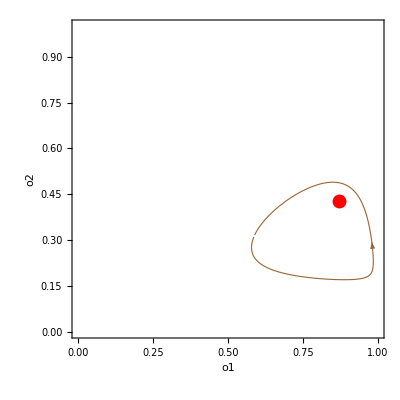

```mathematica
With[{p=-2.97092},
Show[
DisplayPhasePortrait[CTRNN2oHPoff/.θ1->p,SaddleManifolds->True,SaddleManifoldDuration->350,PlotRange->{{0,1},{0,1}}],
DisplayTrajectories[CTRNN2oHPoff/.θ1->p,{Last[First[$Trajectories]]},46.2]]]//Quiet
```

```mathematica
LC=FindLimitCycle[CTRNN2oHPoff/.θ1->-2.97092,Last[First[$Trajectories]],46.2]
```

LimitCycle[Stable,46.3263,{0.58856,0.316175}]

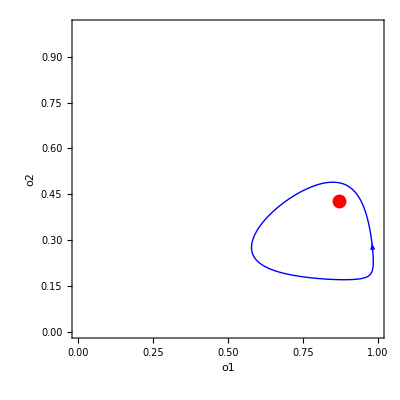

```mathematica
DisplayPhasePortrait[CTRNN2oHPoff/.θ1->-2.97092,LimitSets->{LC}]
```

```mathematica
LCB=FollowLimitCycleBranch[%,θ1,MaxStepSize->0.001];
```

```mathematica
DisplayBifurcationDiagram[CTRNN2oHPoff,θ1,MaxSteps->Infinity,LimitCycleBranches->{LCB},PlotRange->{{-6,1},{0,1},{0,1}},AxesStyle->Directive[Black,12]]
```